```mathematica
Print["Se grafica la solición analítica."]
```

Se grafica la solición analítica.

```mathematica
(*Definición de la solución exacta*)uExact[x_,t_]:=Sin[Pi x] Cos[Pi t];

Plot3D[uExact[x,t],{x,0,1},{t,0,2},AxesLabel->{"x","t","u"},Mesh->None,PlotRange->All,PlotLabel->"Superficie  u(x,t) = sin(π x) cos(π t)",ImageSize->Large,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Animate[Plot[uExact[x,t],{x,0,1},PlotRange->{-1,1},AxesLabel->{"x","u"},PlotLabel->Row[{"Perfil espacial  (t = ",NumberForm[t,{2,2}]," s)"}]],{t,0,2},AnimationRate->0.2]
```

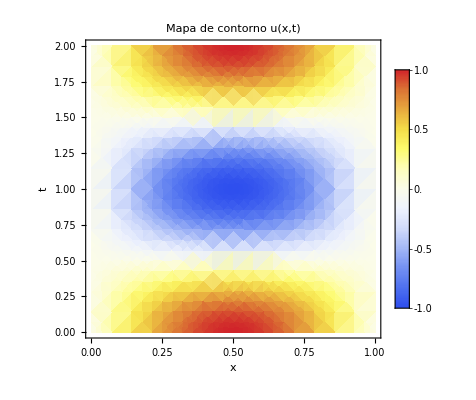

```mathematica
DensityPlot[uExact[x,t],{x,0,1},{t,0,2},FrameLabel->{"x","t"},PlotLabel->"Mapa de contorno  u(x,t)",ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```